```mathematica
(*Multiplier-Accelerator: Discrete (c) Lucie Davidova, Josef Strasky, Jan Capek 2013, Jan Vavra & Alessandra Lanzafame 2014*)
Manipulate[
{{ListPlot[RecurrenceTable[{y[t]-(1+v)*c*y[t-1]+v*c*y[t-2]==c0+I0,{y[0]==1,y[1]==10}},y,{t,0,100}], Filling->Axis, PlotRange -> All, ImageSize->500, PlotMarkers->{"•", 9}],Show[ListPlot[{{v,c}},PlotStyle->{Red,PointSize[0.03]}], ContourPlot[c-4 v+2 c v+c v^2==0,{v,0,5},{c,0,1}],PlotRange->{{0,5},{0,1}},ImageSize->500]},{"Equlibrium Y*="<>ToString[If[c==1,"none",(-c0-I0)/(-1+c)]],""},
{"r = "<>ToString[1/2 (c+c v-√c √(c-4 v+2 c v+c v^2))],""},
{"s = "<>ToString[1/2 (c+c v+√c √(c-4 v+2 c v+c v^2))],""},
{"Solution is "<> ToString[If[c>(4v)/(1+v)^2,"non-cyclical", If[Sqrt[(1/2*(c+c*v))^2+Abs[1/4 c *(c-4 v+2 c v+c v^2)]]<=1,If[Sqrt[(1/2*(c+c*v))^2+Abs[1/4 c *(c-4 v+2 c v+c v^2)]]==1,"cyclical stable","cyclical converging" ],"cyclical explosive"]]], ""},
{If[ c<(4v)/(1+v)^2," R = "<>ToString[Sqrt[(1/2*(c+c*v))^2+Abs[1/4 c *(c-4 v+2 c v+c v^2)]]],""],""}}//MatrixForm,
{{c,0.9,"c - propensity to consume - MULTIPLIER"},.1,1,Appearance->"Labeled"}, {{v,1,"v - propensity to invest - ACCELERATOR"},0.1,5,Appearance->"Labeled"},
{{c0,1,"autonomous consumption"},0.1,2,Appearance->"Labeled"},
{{I0,1,"autonomous investments"},0.1,2,Appearance->"Labeled"}]
```

```mathematica
(*Equilibrium*)
Solve[y-(1+v)*c*y+v*c*y==I0+c0,y]
```

{{y→(-c0-I0)/(-1+c)}}

```mathematica
(*Characteristic polynomial*)
Solve[y^2-(1+v)*c*y+v*c==0,y]
```

{{y→1/2 (c+c v-√c √(c-4 v+2 c v+c v^2))},{y→1/2 (c+c v+√c √(c-4 v+2 c v+c v^2))}}

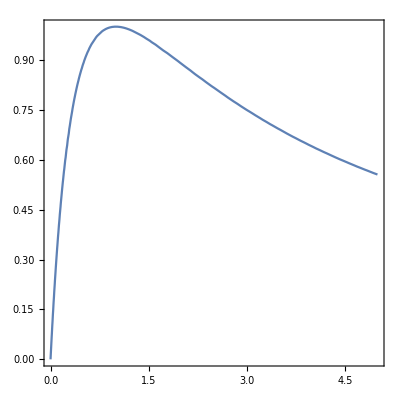

```mathematica
ContourPlot[c-4 v+2 c v+c v^2==0,{v,0,5},{c,0,1}]
```